```mathematica
Shapes 3
```

```mathematica
i2={1,0};
j2={0,1};
i3={1,0,0};
j3={0,1,0};
k3={0,0,1};
```

```mathematica
Question 1
```

```mathematica
x1=1.5;
y1=1.5;
R=1;
```

```mathematica
x=R*Sin[t]+x1;
y=R*Cos[t]+y1;
```

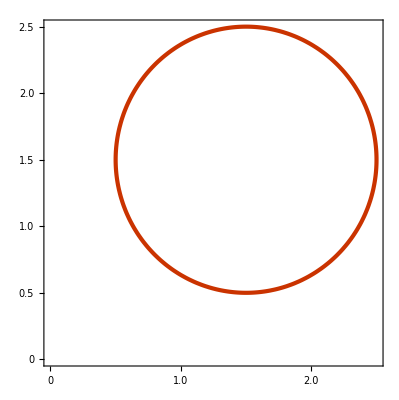

```mathematica
ParametricPlot[{x,y},{t,0,2Pi},PlotTheme->"Web",AxesOrigin->{0,0}]
```

```mathematica
r=x*i2+y*j2
r'=D[r,t]
Integrate[Norm[r'],{t,0,2Pi}]
```

{1.5+Sin[t],1.5+Cos[t]}

{Cos[t],-Sin[t]}

2 π

```mathematica
Question 2
```

```mathematica
Clear["Global`*"]
i2={1,0};
j2={0,1};
i3={1,0,0};
j3={0,1,0};
k3={0,0,1};
```

```mathematica
x1=1.5;
y1=1.5;
a=3;
b=2;
```

```mathematica
x=a*Sin[t]+x1;
y=b*Cos[t]+y1;
```

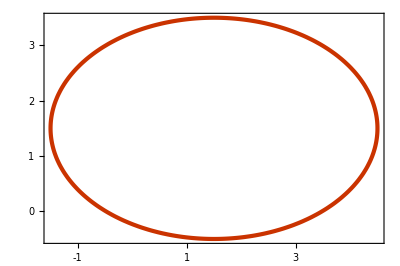

```mathematica
ParametricPlot[{x,y},{t,0,2Pi},PlotTheme->"Web",AxesOrigin->{0,0}]
```

```mathematica
r=x*i2+y*j2;
r'=D[r,t];
N@Integrate[Norm[r'],{t,0,2Pi}]
```

15.8654

```mathematica
"Unit Normal";
T=r'/Norm[r']
T'=D[T,t];
N1=T'/Norm[T'];
Simplify[N1]
```

{(3 Cos[t])/(√(9 Abs[Cos[t]]^2+4 Abs[Sin[t]]^2)),-(2 Sin[t])/(√(9 Abs[Cos[t]]^2+4 Abs[Sin[t]]^2))}

{-((3 (9 Abs[Cos[t]]^2 Sin[t]-9 Abs[Cos[t]] Cos[t] Sin[t] Abs'[Cos[t]]+4 Abs[Sin[t]] (Abs[Sin[t]] Sin[t]+Cos[t]^2 Abs'[Sin[t]])))/(√(9 Abs[9 Abs[Cos[t]]^2 Sin[t]-9 Abs[Cos[t]] Cos[t] Sin[t] Abs'[Cos[t]]+4 Abs[Sin[t]] (Abs[Sin[t]] Sin[t]+Cos[t]^2 Abs'[Sin[t]])]^2+4 Abs[9 Abs[Cos[t]]^2 Cos[t]+9 Abs[Cos[t]] Sin[t]^2 Abs'[Cos[t]]+4 Abs[Sin[t]] Cos[t] (Abs[Sin[t]]-Sin[t] Abs'[Sin[t]])]^2))),-((2 (9 Abs[Cos[t]]^2 Cos[t]+9 Abs[Cos[t]] Sin[t]^2 Abs'[Cos[t]]+4 Abs[Sin[t]] Cos[t] (Abs[Sin[t]]-Sin[t] Abs'[Sin[t]])))/(√(9 Abs[9 Abs[Cos[t]]^2 Sin[t]-9 Abs[Cos[t]] Cos[t] Sin[t] Abs'[Cos[t]]+4 Abs[Sin[t]] (Abs[Sin[t]] Sin[t]+Cos[t]^2 Abs'[Sin[t]])]^2+4 Abs[9 Abs[Cos[t]]^2 Cos[t]+9 Abs[Cos[t]] Sin[t]^2 Abs'[Cos[t]]+4 Abs[Sin[t]] Cos[t] (Abs[Sin[t]]-Sin[t] Abs'[Sin[t]])]^2)))}

```mathematica
Question 3
```

```mathematica
Clear["Global`*"]
i2={1,0};
j2={0,1};
i3={1,0,0};
j3={0,1,0};
k3={0,0,1};
```

```mathematica
r[u_]:=a*Exp[b*u]*Cos[u]*i2+a*Exp[b*u]*Sin[u]*j2
```

50

-0.1

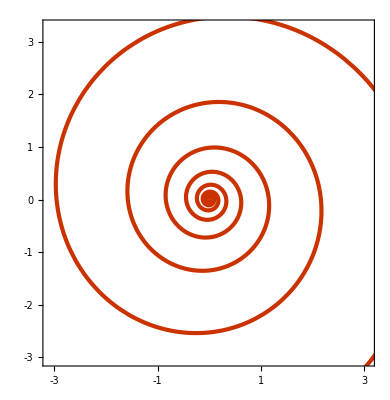

```mathematica
a=50
b=-.1
ParametricPlot[r[u],{u,0,100},PlotTheme->"Web"]
```

```mathematica
T=r'[u]/Norm[r'[u]];
N1=D[T,u]/Norm[D[T,u]];
```

a makes the spiral larger

b dictates how tight the spiral is

u is the location of the sprial

```mathematica
Integrate[Norm[r'[u]],{u,0,Infinity}]
```

502.494

```mathematica
Question 4
```

```mathematica
Clear["Global`*"]
i2={1,0};
j2={0,1};
i3={1,0,0};
j3={0,1,0};
k3={0,0,1};
```

```mathematica
r[u_]=a*Cos[u]*i3+a*Sin[u]*j3+b*u*k3
```

{a Cos[u],a Sin[u],b u}

```mathematica
a=1
b=.1
ParametricPlot3D[r[u],{u,0,10Pi}]
```

1

0.1

-Graphics3D-

```mathematica
T=r'[u]/Norm[r'[u]]
```

{-Sin[u]/(√(0.01+Abs[Cos[u]]^2+Abs[Sin[u]]^2)),Cos[u]/(√(0.01+Abs[Cos[u]]^2+Abs[Sin[u]]^2)),0.1/(√(0.01+Abs[Cos[u]]^2+Abs[Sin[u]]^2))}

a is the diameter of the spiral

b makes the spiral heigher or lower

u determines the number of spirals

```mathematica
Integrate[Norm[r'[u]],{u,0,10Pi}]
```

31.5726

```mathematica
Question 5
```

```mathematica
Clear["Global`*"]
i2={1,0};
j2={0,1};
i3={1,0,0};
j3={0,1,0};
k3={0,0,1};
```

```mathematica
r[u_]:=u*i2+(Abs[u]^n-1)*j2
```

1

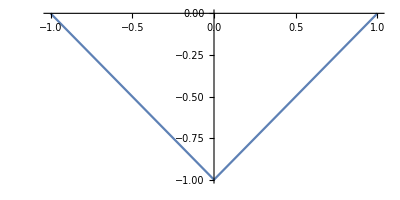

```mathematica
n=1
ParametricPlot[r[u],{u,-1,1}]
```

```mathematica
Integrate[Norm[r'[u]],{u,-1,1}]
```

2 √2

```mathematica
Integrate[1,{x,-1,1},{y,Abs[x]^n-1,d}]
```

1+2 d

```mathematica
Solve[Sqrt[2]==1+2d,d]
```

{{d→1/2 (-1+√2)}}

```mathematica
Integrate[Norm[r'[u]],{u,-1,1}]
```

2 √2

```mathematica
Question 6
```

```mathematica
Clear["Global`*"]
i2={1,0};
j2={0,1};
i3={1,0,0};
j3={0,1,0};
k3={0,0,1};
```

```mathematica
a1={0,0};
a2={1,1};
```

```mathematica
r[u_]=(1-u)a1+u*a2
```

{u,u}

```mathematica
pts={r[0],r[1/2],r[1]}
```

{{0,0},{1/2,1/2},{1,1}}

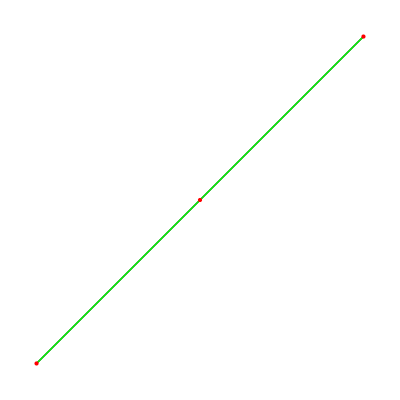

```mathematica
Graphics[{BezierCurve[pts],Green,Line[pts],Red,Point[pts]}]
```

```mathematica
Question 7
```

```mathematica
Clear["Global`*"]
i2={1,0};
j2={0,1};
i3={1,0,0};
j3={0,1,0};
k3={0,0,1};
```

```mathematica
a1={0,0};
a2={0,3};
a3={4,5};
```

```mathematica
r[u_]:=(1-u)^2 a1+2*u*(1-u)a2+u^2*a3
```

```mathematica
pts={r[0],r[1/3],r[1]}
```

{{0,0},{4/3,17/9},{4,5}}

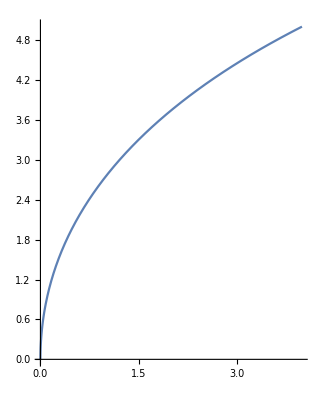

```mathematica
ParametricPlot[r[u],{u,0,1}]
```

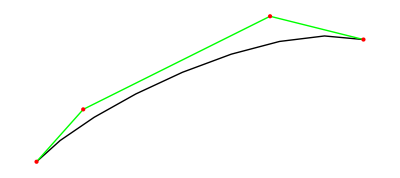

```mathematica
Graphics[{BezierCurve[pts],Green,Line[pts],Red,Point[pts]}]
```

```mathematica
Question 8
```

```mathematica
Clear["Global`*"]
i2={1,0};
j2={0,1};
i3={1,0,0};
j3={0,1,0};
k3={0,0,1};
```

```mathematica
a1={0,0};
a2={1,2};
a3={2,1};
a4={2,2};
```

```mathematica
r[u_]:=(1-u)^3*a1+3*u*(1-u)^2*a2+3*u^2*(1-u)*a3+u^3*a4
```

```mathematica
pts={r[0],r[.1],r[-.3],r[1]}
Graphics[{BezierCurve[pts],Green,Line[pts],Red,Point[pts]}]
```

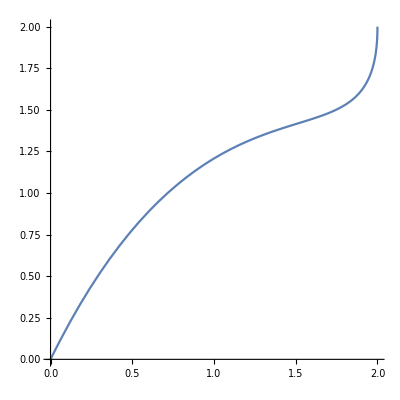

```mathematica
ParametricPlot[r[u],{u,0,1}]
```

```mathematica
Question 9
```

```mathematica
Clear["Global`*"]
i2={1,0};
j2={0,1};
i3={1,0,0};
j3={0,1,0};
k3={0,0,1};
```

```mathematica
a=4;
R=1;
r[u_,v_]:=(a+R*Cos[u])*Cos[v]*i3+(a+R*Cos[u])*Sin[v]*j3+R*Sin[u]*k3
```

```mathematica
ParametricPlot3D[r[u,v],{u,0,2π},{v,0,2π}]
```

-Graphics3D-

```mathematica
du=D[r[u,v],u];
dv=D[r[u,v],v];
cross=Cross[du,dv];
```

```mathematica
n=cross/Norm[cross];
```

```mathematica
n
```

{(-4 Cos[u] Cos[v]-Cos[u]^2 Cos[v])/(√(Abs[-4 Cos[u] Cos[v]-Cos[u]^2 Cos[v]]^2+Abs[-4 Cos[u] Sin[v]-Cos[u]^2 Sin[v]]^2+Abs[-4 Cos[v]^2 Sin[u]-Cos[u] Cos[v]^2 Sin[u]-4 Sin[u] Sin[v]^2-Cos[u] Sin[u] Sin[v]^2]^2)),(-4 Cos[u] Sin[v]-Cos[u]^2 Sin[v])/(√(Abs[-4 Cos[u] Cos[v]-Cos[u]^2 Cos[v]]^2+Abs[-4 Cos[u] Sin[v]-Cos[u]^2 Sin[v]]^2+Abs[-4 Cos[v]^2 Sin[u]-Cos[u] Cos[v]^2 Sin[u]-4 Sin[u] Sin[v]^2-Cos[u] Sin[u] Sin[v]^2]^2)),(-4 Cos[v]^2 Sin[u]-Cos[u] Cos[v]^2 Sin[u]-4 Sin[u] Sin[v]^2-Cos[u] Sin[u] Sin[v]^2)/(√(Abs[-4 Cos[u] Cos[v]-Cos[u]^2 Cos[v]]^2+Abs[-4 Cos[u] Sin[v]-Cos[u]^2 Sin[v]]^2+Abs[-4 Cos[v]^2 Sin[u]-Cos[u] Cos[v]^2 Sin[u]-4 Sin[u] Sin[v]^2-Cos[u] Sin[u] Sin[v]^2]^2))}

```mathematica
ParametricPlot3D[n,{u,0,2Pi},{v,0,2Pi}]
```

-Graphics3D-

```mathematica
Integrate[Norm[cross],{u,0,2π},{v,0,2π}]
```

16 π^2

```mathematica
Question 10
```

```mathematica
Clear["Global`*"]
i2={1,0};
j2={0,1};
i3={1,0,0};
j3={0,1,0};
k3={0,0,1};
```

```mathematica
x[x_]:=x
z[x_]:=-H+H*(16/L^4)*x^4
y[x_]:=(W/2)(4/L^2)x^2-(W/2)Sqrt[(z[u]+H)/H]
r[u_,v_]:=x[v]*i3+y[v]*j3+z[u]*k3
```

```mathematica
W=10
L=30
H=10
r[u]
ParametricPlot3D[r[u,v],{u,-100,100},{v,-100,100}]
```

10

30

10

r[u]

-Graphics3D-